```mathematica
Quit[];
```

```mathematica
(*healthy state*)
Wss=0;
Wgs=1.12;
Wsg=19;
Wgg=6.6;
Wcs=2.42;
Wxg=15.1;
Ctx=27;
Str=2;
Ms = 300;
Mg = 400;
Bs = 17;
Bg = 75;
tauS= 6;(* tau_s = tau_g *);
```

```mathematica
(* Rescaled System's coefficients and function definition *)
ac=Wss;
bc=-Wgs;
cc=Wsg;
dc=-Wgg;
tu=Wcs*Ctx;
tv=-Wxg*Str;
f1[in1_]:=Ms/(1+Exp[-4*in1/Ms]*(Ms-Bs)/Bs);
f2[in2_]:=Mg/(1+Exp[-4*in2/Mg]*(Mg-Bg)/Bg);
F[u_,ud_]:={
-u[[1]]+f1[tu+ac*ud[[1]]+bc*ud[[2]]],
-u[[2]]+f2[tv+cc*ud[[1]]+dc*ud[[2]]]}
```

```mathematica
(*equilibrium point*)
eq={u,v}/.FindRoot[F[{u,v},{u,v}]=={0,0},{{u,0},{v,0}}]
```

{18.1475,53.693}

```mathematica
(*characteristic parameter values*)
alpha=ac*f1'[tu+ac*eq[[1]]+bc*eq[[2]]]+dc*f2'[tv+cc*eq[[1]]+dc*eq[[2]]]
beta=(ac*dc-bc*cc)*f1'[tu+ac*eq[[1]]+bc*eq[[2]]]*f2'[tv+cc*eq[[1]]+dc*eq[[2]]]
```

-3.06805

2.24878

```mathematica
(*verify the position of the point (alpha,beeta) with respect to the parabola alpha^2=4 beta -> the point is BELOW the parabola*)
beta-alpha^2/4
```

-0.104454

```mathematica
(*Dirac kernel - Laplace transform and related functions defined in paper*)
H[z_]:=Exp[-z];
Q[t_,z_]:=(z+t)/(t*H[z]);
al[t_,w_]:=2*Re[Q[t,I*w]];
be[t_,w_]:=Abs[Q[t,I*w]]^2;
Co[t_,w_]:=Re[H[I*w]];
rho[w_]:=1; (*given explicitely for ease of computation*)
theta[w_]:=w; (*given explicitely for ease of computation*)
w1[t_]:=w/.FindRoot[Im[Q[t,I*w]]==0,{w,Pi/2,Pi}];
mu[w_]:=1/(rho[w]*Cos[theta[w]]);
```

```mathematica
(*Use Theorem 2.8 for the Dirac kernel, to detect critical value of time delay and frequency - along the line (l_tau)*)
(*find possible values of mu_tau*)
mutau=x/.Solve[{beta==x*(alpha-x),x<-1},x];
(*find possible value of frequency w1 in the interval (Pi/2,Pi) according to Lemma 2.4 *)
wtau=Min[Table[w/.NSolve[{mu[w]==mutau[[k]],Pi/2<w<Pi},w][[1]],{k,1,Length[mutau]}]]
```

2.13938

```mathematica
(*find critical value of tau based on the formula of w_tau from Theorem 2.8 *)
Tau=tau/.Solve[wtau*Cos[theta[wtau]]+tau*Sin[theta[wtau[[]]]]==0,tau][[1]]
```

1.367

```mathematica
(*predicted frequency of oscillations at Hopf bifurcation - divided by Tau due to relation between \Delta and \hat{\Delta}*)
freq=wtau/(Tau*2*Pi)
```

0.24908

```mathematica
(*frequency for the healthy state at bifurcation - rescaled - in Hz*)
freq/(tauS*10^(-3))
```

41.5133

```mathematica
(*stability region for Dirac kernel, together with point of coordinates (alpha, beta) - uses range accoring to bifurcation values, so that domains can be compared*)
pd[t_]:=
Show[RegionPlot[y>1/Co[t,w1[t]]*(x-1/Co[t,w1[t]])&&y>x-1&&x<2(Cos[t*Sqrt[y-1]]-Sqrt[y-1]*Sin[t*Sqrt[y-1]]),{x,2*mu[w1[t]],2},{y,mu[w1[t]],0.96*mu[w1[t]]^2},PlotPoints->100],
Plot[x-1,{x,1+1/Co[t,w1[t]],2},PlotStyle->Red],
Graphics[{Red,PointSize[0.04],Point[{alpha,beta}]}],
LabelStyle->Directive[Bold,Black, FontSize->20],ImageSize->{Automatic,300},
Epilog->Inset[Framed[Style[Row[{"Dirac, τ=",t}],Bold,20],Background->LightYellow,RoundingRadius->4],{1+mu[w1[Tau]],0.85*mu[w1[Tau]]^2}],
PlotRange->{{2*mu[w1[Tau]],2},{mu[w1[Tau]],0.96*mu[w1[Tau]]^2}}]
```

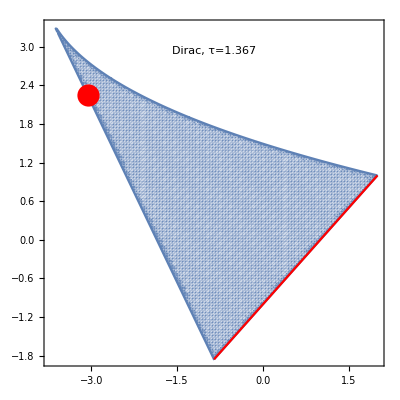

```mathematica
pd[Tau]
```

```mathematica
(*system with DIRAC kernel*)
sys[tau_]:={u'[t]==F[{u[t],v[t]},{u[t-tau],v[t-tau]}][[1]],
v'[t]==F[{u[t],v[t]},{u[t-tau],v[t-tau]}][[2]],
 u[t /; t≤ 0]==0,
v[t /; t≤ 0]==0};
```

```mathematica
(*frequency at Hopf bifurcation computed based on the numerically evaluated solution - agrees with theoretically calculated value*)
Tmax=2000;
pts[tau_]:=Reap[s=NDSolve[{u'[t]==F[{u[t],v[t]},{u[t-tau],v[t-tau]}][[1]],
v'[t]==F[{u[t],v[t]},{u[t-tau],v[t-tau]}][[2]],
 u[t /; t≤ 0]==eq[[1]]*1.1,
v[t /; t≤ 0]==eq[[2]]*1.1,WhenEvent[v'[t]==0,Sow[t]]},{v,v'},{t,Tmax*0.8,Tmax}]][[2,1]];
frequency[tau_]:=1/Mean[Differences[pts[tau],1,2]]
```

```mathematica
(*frequency comupter numerically at bifurcation - rescaled - in Hz*)
frequency[1.967]/(tauS*10^(-3))
```

30.0081

```mathematica
pfreqhealthy=Table[{del,frequency[del]/(tauS*10^(-3))},{del,Tau,2.2,0.05}];
```

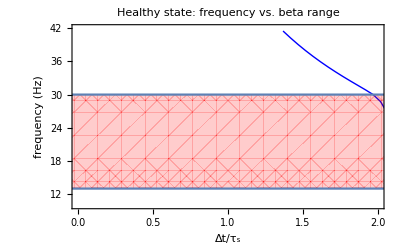

```mathematica
Show[ListPlot[pfreqhealthy,Joined->True,PlotRange->All,PlotStyle->{Thick,Blue}],RegionPlot[13<y<30,{x,-0.5,2.5},{y,10,90},PlotStyle->{Red,Opacity[0.2]}],
FrameLabel->{"Δt/τ_s","frequency (Hz)"},Frame->True,Axes->False,PlotRange->{{0,2},{10,42}},PlotLabel->"Healthy state: frequency vs. beta range"]
```

```mathematica
(*plot evolution of state variables*)
trans=0;Tmax=600/1.2;
p1[tau_]:=Plot[Evaluate[{u[(t+trans)/(tauS*10^(-3))],v[(t+trans)/(tauS*10^(-3))]} /. NDSolve[sys[tau],{u,v},{t,Tmax}]],{t,0,(Tmax-trans)*tauS*10^(-3)},PlotRange->All,Axes->False,Frame->True, PlotStyle->{{Thick,Red},{Thick,Blue}},FrameLabel->{None,"STN, GP vs. time (s)"},ImageSize->{Automatic,300},LabelStyle->Directive[Bold,Black, FontSize->20]]
```

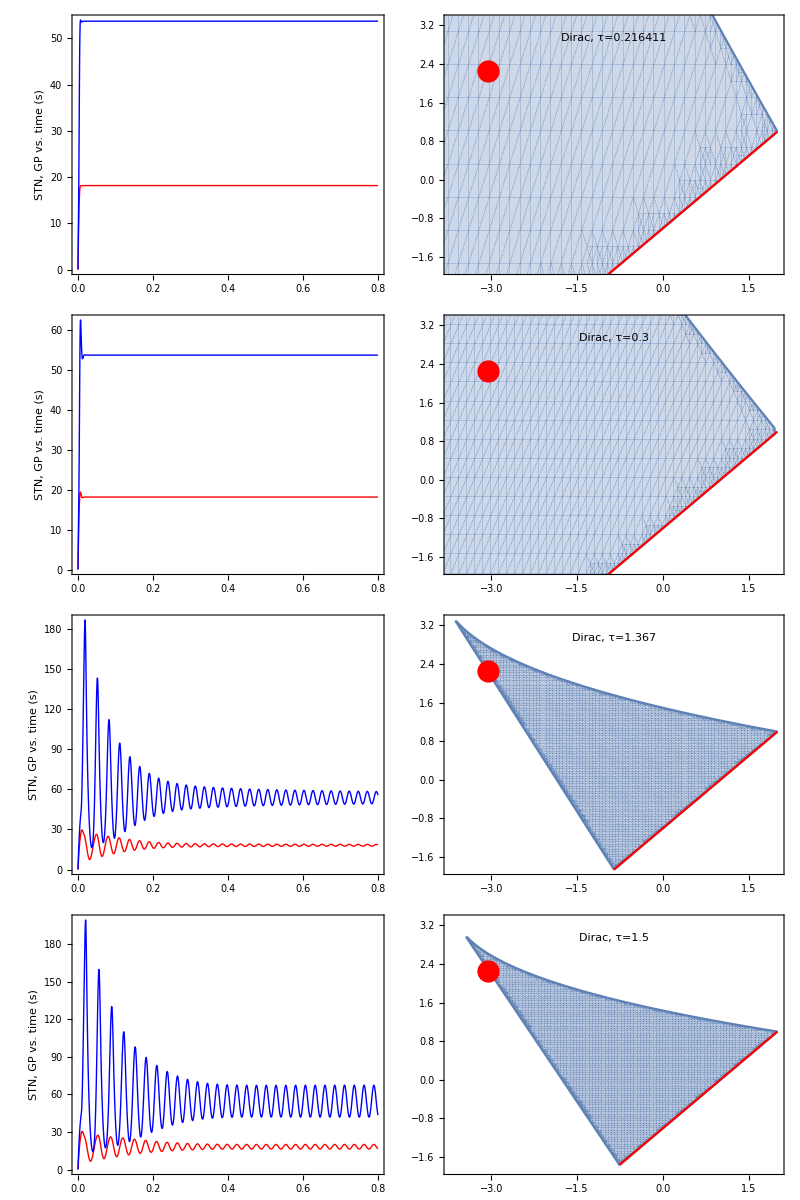

```mathematica
(*Graphics: evolution of state variables vs. stability domain*)
Grid[{{p1[0.216411],pd[0.216411]},{p1[0.3],pd[0.3]},{p1[Tau],pd[Tau]},{p1[1.5],pd[1.5]}}]
```